## Check API

```mathematica
apiData=CloudLoggingData[CloudObject[["https://www.wolframcloud.com/obj/josephb/Scrabble/APIs/FindViablePlays"](https://www.wolframcloud.com/obj/josephb/Scrabble/APIs/FindViablePlays)]]
```

<|LastDay→<|TotalCalls→6014,TotalCredits→8308,CallRateTimeSeries→TimeSeries[…]|>,LastWeek→<|TotalCalls→12127,TotalCredits→27209,CallRateTimeSeries→TimeSeries[…]|>,LastMonth→<|TotalCalls→16112,TotalCredits→43429,CallRateTimeSeries→TimeSeries[…]|>,All→<|TotalCalls→16112,TotalCredits→43429,CallRateTimeSeries→TemporalData[TimeSeries, «1»]|>|>

```mathematica
apiData[All]["CallRateTimeSeries"]
```

TemporalData[TimeSeries, «1»]

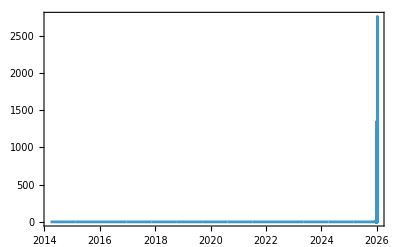

```mathematica
DateListPlot[apiData[All]["CallRateTimeSeries"]]
```

Bug

## Load Paclet

```mathematica
SetDirectory[NotebookDirectory[]];
PacletDirectoryLoad[Directory[]];
Get["Scrabbology`"]
```

## UpdateTileBag

```mathematica
initialTileBag=
URLEncode[
"{\"A\":9,\"B\":2,\"C\":2,\"D\":4,\"E\":12,\"F\":2,\"G\":3,\"H\":2,\"I\":9,\"J\":1,\"K\":1,\"L\":4,\"M\":2,\"N\":6,\"O\":8,\"P\":2,\"Q\":1,\"R\":6,\"S\":4,\"T\":6,\"U\":4,\"V\":2,\"W\":2,\"X\":1,\"Y\":2,\"Z\":1,\"?\":2}"
];
UpdateTileBag[ImportString[URLDecode[initialTileBag],"RawJSON"],"ENJAMBS",2]
```

{success→True,tileBag→{A→8,B→1,C→2,D→4,E→11,F→2,G→3,H→2,I→9,J→0,K→1,L→4,M→1,N→5,O→8,P→2,Q→1,R→6,S→3,T→6,U→4,V→2,W→2,X→1,Y→2,Z→1,?→2},blanks→{}}

```mathematica
CloudDeploy[
APIFunction[
{"tileBag"->"String","bingo"->"String","blanksRemaining"->"Integer"},
UpdateTileBag[
ImportString[URLDecode[#tileBag],"RawJSON"],
#bingo,
#blanksRemaining
]&,
"JSON"
],
"Scrabble/APIs/UpdateTileBag",
Permissions->"Public"
]
```

CloudObject[https://www.wolframcloud.com/obj/josephb/Scrabble/APIs/UpdateTileBag]

### Test API

```mathematica
URLExecute[
"https://www.wolframcloud.com/obj/josephb/Scrabble/APIs/UpdateTileBag",
{"tileBag"->initialTileBag,"bingo"->"ENJAMBS","blanksRemaining"->2}
]
```

{success→True,tileBag→{A→8,B→1,C→2,D→4,E→11,F→2,G→3,H→2,I→9,J→0,K→1,L→4,M→1,N→5,O→8,P→2,Q→1,R→6,S→3,T→6,U→4,V→2,W→2,X→1,Y→2,Z→1,?→2},blanks→{}}

```mathematica
URLExecute[
"https://www.wolframcloud.com/obj/josephb/Scrabble/APIs/UpdateTileBag",
{"tileBag"->initialTileBag,"bingo"->"COZZIES","blanksRemaining"->2}
]
```

{success→True,tileBag→{A→9,B→2,C→1,D→4,E→11,F→2,G→3,H→2,I→8,J→1,K→1,L→4,M→2,N→6,O→7,P→2,Q→1,R→6,S→3,T→6,U→4,V→2,W→2,X→1,Y→2,Z→0,?→1},blanks→{Z}}

```mathematica
URLExecute[
"https://www.wolframcloud.com/obj/josephb/Scrabble/APIs/UpdateTileBag",
{"tileBag"->initialTileBag,"bingo"->"BEZZAZZ","blanksRemaining"->2}
]
```

{success→False,error→CANNOT-FORM-WORD}

## FindViablePlays

### Deploy API

```mathematica
CloudDeploy[
APIFunction[
{"bingo"->"String","turns"->"String"},
FindViablePlays[
#bingo,
ImportString[URLDecode[#turns],"RawJSON"]
]&,
"JSON"
],
"Scrabble/APIs/FindViablePlays",
Permissions->"Public"
]
```

CloudObject[https://www.wolframcloud.com/obj/josephb/Scrabble/APIs/FindViablePlays]

## Cull Word List

```mathematica
words=Import["C:\\Users\\josephb\\PersonalProjects\\scrabble\\perfectscrabblegames\\src\\assets\\EightLetterBingos.txt","List"];
```

```mathematica
tiles="ADEGGSTT";
```

```mathematica
c1=CullBingoList[words,tiles,0];
```

```mathematica
Length[DeleteDuplicates[c1]]
```

3

```mathematica
c2=CullBingoList[words,tiles,1];
```

```mathematica
Length[DeleteDuplicates[c2]]
```

141

```mathematica
Dataset[DeleteDuplicates[c2]]
```

## Test 13/14

```mathematica
CloudObject["https://www.wolframcloud.com/env/josephb/Scrabble/PerfectScrabbleGameDatabase"]
```

CloudObject[https://www.wolframcloud.com/env/josephb/Scrabble/PerfectScrabbleGameDatabase]

```mathematica
game=Import[CloudObject["https://www.wolframcloud.com/env/josephb/Scrabble/PerfectScrabbleGames"]][[11]]
```

<|1→<|Bingo→AGEISMS,Position→{H,2},Direction→Right|>,2→<|Bingo→WHIPSAWS,Position→{A,6},Direction→Down,Overlap→S|>,3→<|Bingo→OOZINESS,Position→{A,8},Direction→Down,Overlap→S|>,4→<|Bingo→LOGJUICE,Position→{A,4},Direction→Down,Overlap→E|>,5→<|Bingo→SAVANNAH,Position→{G,8},Direction→Right,Overlap→S|>,6→<|Bingo→GLYCOGEN,Position→{H,3},Direction→Down,Overlap→G|>,7→<|Bingo→ORATORIO,Position→{A,8},Direction→Right,Overlap→O|>,8→<|Bingo→MILITARY,Position→{H,7},Direction→Down,Overlap→M|>,9→<|Bingo→IRRITATE,Position→{H,5},Direction→Down,Overlap→I|>,10→<|Bingo→DIATRETA,Position→{A,2},Direction→Down,Overlap→A|>,11→<|Bingo→UNBANKED,Position→{D,14},Direction→Down,Overlap→A|>,12→<|Bingo→REBUFFED,Position→{N,7},Direction→Right,Overlap→R|>,13→<|Bingo→VOLVOXES,Position→{D,10},Direction→Down,Overlap→V|>,14→<|Bingo→QUEENDOM,Position→{C,12},Direction→Down,Overlap→N|>|>

```mathematica
bingos={"AGEISMS","WHIPSAW","OOZINES","LOGJUIC","AVANNAH","LYCOGEN","RATORIO","ILITARY","RRITATE","DIATRET","UNBNKED","EBUFFED","VOLOXE?","QUEED?M"};
takeLists=Table[Take[bingos,n],{n,Length[bingos]}];
tileBags=editTileBag/@takeLists;
```

```mathematica
editScrabbleGameSchema[game_]:=
Module[
{gameWithID,gameWithLowercaseKeys,gameWithRowCol,gameWithDirections},
gameWithID=
Map[
Prepend[#,"id"->Position[Values[game],#][[1,1]]]&,
Values[game]
];
gameWithLowercaseKeys=
Map[
KeyMap[ToLowerCase,#]&,
gameWithID
];
gameWithRowCol=
Map[
With[
{pos=#position},
{row=LetterNumber[pos[[1]]]-1, col=pos[[2]]-1},
KeyDrop[Append[#,{"row"->row,"col"->col}],"position"]
]&,
gameWithLowercaseKeys
];
gameWithDirections=
Map[
If[#direction=="Right",ReplacePart[#,"direction"->"H"],ReplacePart[#,"direction"->"V"]]&,
gameWithRowCol
]
]
```

```mathematica
newGame=
MapThread[
Append[#1,{"tileBag"->#2,"tilesLeft"->Total[Values[#2]]}]&,
{
editScrabbleGameSchema[game],
tileBags
}
]
```

{<|id→1,bingo→AGEISMS,direction→H,row→7,col→1,tileBag→<|A→8,B→2,C→2,D→4,E→11,F→2,G→2,H→2,I→8,J→1,K→1,L→4,M→1,N→6,O→8,P→2,Q→1,R→6,S→2,T→6,U→4,V→2,W→2,X→1,Y→2,Z→1,?→2|>,tilesLeft→93|>,<|id→2,bingo→WHIPSAWS,direction→V,overlap→S,row→0,col→5,tileBag→<|A→7,B→2,C→2,D→4,E→11,F→2,G→2,H→1,I→7,J→1,K→1,L→4,M→1,N→6,O→8,P→1,Q→1,R→6,S→1,T→6,U→4,V→2,W→0,X→1,Y→2,Z→1,?→2|>,tilesLeft→86|>,<|id→3,bingo→OOZINESS,direction→V,overlap→S,row→0,col→7,tileBag→<|A→7,B→2,C→2,D→4,E→10,F→2,G→2,H→1,I→6,J→1,K→1,L→4,M→1,N→5,O→6,P→1,Q→1,R→6,S→0,T→6,U→4,V→2,W→0,X→1,Y→2,Z→0,?→2|>,tilesLeft→79|>,<|id→4,bingo→LOGJUICE,direction→V,overlap→E,row→0,col→3,tileBag→<|A→7,B→2,C→1,D→4,E→10,F→2,G→1,H→1,I→5,J→0,K→1,L→3,M→1,N→5,O→5,P→1,Q→1,R→6,S→0,T→6,U→3,V→2,W→0,X→1,Y→2,Z→0,?→2|>,tilesLeft→72|>,<|id→5,bingo→SAVANNAH,direction→H,overlap→S,row→6,col→7,tileBag→<|A→4,B→2,C→1,D→4,E→10,F→2,G→1,H→0,I→5,J→0,K→1,L→3,M→1,N→3,O→5,P→1,Q→1,R→6,S→0,T→6,U→3,V→1,W→0,X→1,Y→2,Z→0,?→2|>,tilesLeft→65|>,<|id→6,bingo→GLYCOGEN,direction→V,overlap→G,row→7,col→2,tileBag→<|A→4,B→2,C→0,D→4,E→9,F→2,G→0,H→0,I→5,J→0,K→1,L→2,M→1,N→2,O→4,P→1,Q→1,R→6,S→0,T→6,U→3,V→1,W→0,X→1,Y→1,Z→0,?→2|>,tilesLeft→58|>,<|id→7,bingo→ORATORIO,direction→H,overlap→O,row→0,col→7,tileBag→<|A→3,B→2,C→0,D→4,E→9,F→2,G→0,H→0,I→4,J→0,K→1,L→2,M→1,N→2,O→2,P→1,Q→1,R→4,S→0,T→5,U→3,V→1,W→0,X→1,Y→1,Z→0,?→2|>,tilesLeft→51|>,<|id→8,bingo→MILITARY,direction→V,overlap→M,row→7,col→6,tileBag→<|A→2,B→2,C→0,D→4,E→9,F→2,G→0,H→0,I→2,J→0,K→1,L→1,M→1,N→2,O→2,P→1,Q→1,R→3,S→0,T→4,U→3,V→1,W→0,X→1,Y→0,Z→0,?→2|>,tilesLeft→44|>,<|id→9,bingo→IRRITATE,direction→V,overlap→I,row→7,col→4,tileBag→<|A→1,B→2,C→0,D→4,E→8,F→2,G→0,H→0,I→1,J→0,K→1,L→1,M→1,N→2,O→2,P→1,Q→1,R→1,S→0,T→2,U→3,V→1,W→0,X→1,Y→0,Z→0,?→2|>,tilesLeft→37|>,<|id→10,bingo→DIATRETA,direction→V,overlap→A,row→0,col→1,tileBag→<|A→0,B→2,C→0,D→3,E→7,F→2,G→0,H→0,I→0,J→0,K→1,L→1,M→1,N→2,O→2,P→1,Q→1,R→0,S→0,T→0,U→3,V→1,W→0,X→1,Y→0,Z→0,?→2|>,tilesLeft→30|>,<|id→11,bingo→UNBANKED,direction→V,overlap→A,row→3,col→13,tileBag→<|A→0,B→1,C→0,D→2,E→6,F→2,G→0,H→0,I→0,J→0,K→0,L→1,M→1,N→0,O→2,P→1,Q→1,R→0,S→0,T→0,U→2,V→1,W→0,X→1,Y→0,Z→0,?→2|>,tilesLeft→23|>,<|id→12,bingo→REBUFFED,direction→H,overlap→R,row→13,col→6,tileBag→<|A→0,B→0,C→0,D→1,E→4,F→0,G→0,H→0,I→0,J→0,K→0,L→1,M→1,N→0,O→2,P→1,Q→1,R→0,S→0,T→0,U→1,V→1,W→0,X→1,Y→0,Z→0,?→2|>,tilesLeft→16|>,<|id→13,bingo→VOLVOXES,direction→V,overlap→V,row→3,col→9,tileBag→<|A→0,B→0,C→0,D→1,E→3,F→0,G→0,H→0,I→0,J→0,K→0,L→0,M→1,N→0,O→0,P→1,Q→1,R→0,S→0,T→0,U→1,V→0,W→0,X→0,Y→0,Z→0,?→1|>,tilesLeft→9|>,<|id→14,bingo→QUEENDOM,direction→V,overlap→N,row→2,col→11,tileBag→<|A→0,B→0,C→0,D→0,E→1,F→0,G→0,H→0,I→0,J→0,K→0,L→0,M→0,N→0,O→0,P→1,Q→0,R→0,S→0,T→0,U→0,V→0,W→0,X→0,Y→0,Z→0,?→0|>,tilesLeft→2|>}

```mathematica
FindViablePlays["QUEENDOM",Most[newGame]]
```

{<|bingo→QUEENDOM,row→5,col→5,direction→H,playThroughTurn→3,overlapTile→E|>,<|bingo→QUEENDOM,row→5,col→4,direction→H,playThroughTurn→3,overlapTile→E|>,<|bingo→QUEENDOM,row→4,col→3,direction→H,playThroughTurn→3,overlapTile→N|>,<|bingo→QUEENDOM,row→1,col→1,direction→H,playThroughTurn→3,overlapTile→O|>,<|bingo→QUEENDOM,row→4,col→2,direction→H,playThroughTurn→4,overlapTile→U|>,<|bingo→QUEENDOM,row→2,col→11,direction→V,playThroughTurn→5,overlapTile→N|>,<|bingo→QUEENDOM,row→2,col→12,direction→V,playThroughTurn→5,overlapTile→N|>,<|bingo→QUEENDOM,row→14,col→2,direction→H,playThroughTurn→9,overlapTile→E|>,<|bingo→QUEENDOM,row→14,col→1,direction→H,playThroughTurn→9,overlapTile→E|>,<|bingo→QUEENDOM,row→9,col→7,direction→H,playThroughTurn→13,overlapTile→E|>,<|bingo→QUEENDOM,row→9,col→6,direction→H,playThroughTurn→13,overlapTile→E|>,<|bingo→QUEENDOM,row→4,col→3,direction→H,playThroughTurn→13,overlapTile→O|>}

{success→True,viablePlays→{{bingo→QUEENDOM,row→2,col→11,direction→V,overlapTile→N,tileBag→{A→0,B→0,C→0,D→0,E→1,F→0,G→0,H→0,I→0,J→0,K→0,L→0,M→0,N→0,O→0,P→1,Q→0,R→0,S→0,T→0,U→0,V→0,W→0,X→0,Y→0,Z→0,?→0},tilesLeft→2,blanks→{O}}}}

## Test

```mathematica
turns=Import["C:\\Users\\josephb\\PersonalProjects\\scrabble\\test.json","RawJSON"]
```

{<|id→1,bingo→WINESAP,row→7,col→1,direction→H,blanks→{},tileBag→<|A→8,B→2,C→2,D→4,E→11,F→2,G→3,H→2,I→8,J→1,K→1,L→4,M→2,N→5,O→8,P→1,Q→1,R→6,S→3,T→6,U→4,V→2,W→1,X→1,Y→2,Z→1,?→2|>,tilesLeft→93,score→0|>,<|id→2,bingo→FLYBLOWN,row→0,col→3,direction→V,score→0,blanks→{},tileBag→<|A→8,B→1,C→2,D→4,E→11,F→1,G→3,H→2,I→8,J→1,K→1,L→2,M→2,N→5,O→7,P→1,Q→1,R→6,S→3,T→6,U→4,V→2,W→0,X→1,Y→1,Z→1,?→2|>,tilesLeft→86|>,<|id→3,bingo→FIXITIES,row→0,col→5,direction→V,score→0,blanks→{},tileBag→<|A→8,B→1,C→2,D→4,E→10,F→0,G→3,H→2,I→5,J→1,K→1,L→2,M→2,N→5,O→7,P→1,Q→1,R→6,S→3,T→5,U→4,V→2,W→0,X→0,Y→1,Z→1,?→2|>,tilesLeft→79|>,<|id→4,bingo→EMENDATE,row→7,col→4,direction→V,score→0,blanks→{},tileBag→<|A→7,B→1,C→2,D→3,E→8,F→0,G→3,H→2,I→5,J→1,K→1,L→2,M→1,N→4,O→7,P→1,Q→1,R→6,S→3,T→4,U→4,V→2,W→0,X→0,Y→1,Z→1,?→2|>,tilesLeft→72|>,<|id→5,bingo→DUKESHIP,row→0,col→7,direction→V,score→0,blanks→{},tileBag→<|A→7,B→1,C→2,D→2,E→7,F→0,G→3,H→1,I→4,J→1,K→0,L→2,M→1,N→4,O→7,P→1,Q→1,R→6,S→2,T→4,U→3,V→2,W→0,X→0,Y→1,Z→1,?→2|>,tilesLeft→65|>,<|id→6,bingo→KNOTHEAD,row→2,col→7,direction→H,score→0,blanks→{},tileBag→<|A→6,B→1,C→2,D→1,E→6,F→0,G→3,H→0,I→4,J→1,K→0,L→2,M→1,N→3,O→6,P→1,Q→1,R→6,S→2,T→3,U→3,V→2,W→0,X→0,Y→1,Z→1,?→2|>,tilesLeft→58|>,<|id→7,bingo→HOLLOAED,row→5,col→7,direction→H,score→0,blanks→{},tileBag→<|A→5,B→1,C→2,D→0,E→5,F→0,G→3,H→0,I→4,J→1,K→0,L→0,M→1,N→3,O→4,P→1,Q→1,R→6,S→2,T→3,U→3,V→2,W→0,X→0,Y→1,Z→1,?→2|>,tilesLeft→51|>,<|id→8,bingo→DOOMIEST,row→0,col→7,direction→H,score→0,blanks→{},tileBag→<|A→5,B→1,C→2,D→0,E→4,F→0,G→3,H→0,I→3,J→1,K→0,L→0,M→0,N→3,O→2,P→1,Q→1,R→6,S→1,T→2,U→3,V→2,W→0,X→0,Y→1,Z→1,?→2|>,tilesLeft→44|>,<|id→9,bingo→CORNACRE,row→4,col→11,direction→V,score→0,blanks→{},tileBag→<|A→4,B→1,C→0,D→0,E→3,F→0,G→3,H→0,I→3,J→1,K→0,L→0,M→0,N→2,O→2,P→1,Q→1,R→4,S→1,T→2,U→3,V→2,W→0,X→0,Y→1,Z→1,?→2|>,tilesLeft→37|>,<|id→10,bingo→DIGITRON,row→5,col→14,direction→V,score→0,blanks→{},tileBag→<|A→4,B→1,C→0,D→0,E→3,F→0,G→2,H→0,I→1,J→1,K→0,L→0,M→0,N→1,O→1,P→1,Q→1,R→3,S→1,T→1,U→3,V→2,W→0,X→0,Y→1,Z→1,?→2|>,tilesLeft→30|>,<|id→11,bingo→INAURATE,row→7,col→2,direction→V,score→0,blanks→{},tileBag→<|A→2,B→1,C→0,D→0,E→2,F→0,G→2,H→0,I→1,J→1,K→0,L→0,M→0,N→0,O→1,P→1,Q→1,R→2,S→1,T→0,U→2,V→2,W→0,X→0,Y→1,Z→1,?→2|>,tilesLeft→23|>,<|id→12,bingo→BLUEJAYS,row→4,col→9,direction→V,score→0,blanks→{},tileBag→<|A→1,B→0,C→0,D→0,E→1,F→0,G→2,H→0,I→1,J→0,K→0,L→0,M→0,N→0,O→1,P→1,Q→1,R→2,S→0,T→0,U→1,V→2,W→0,X→0,Y→0,Z→1,?→2|>,tilesLeft→16|>,<|id→13,bingo→OVERGREW,row→0,col→1,direction→V,score→0,blanks→{E},tileBag→<|A→1,B→0,C→0,D→0,E→0,F→0,G→1,H→0,I→1,J→0,K→0,L→0,M→0,N→0,O→0,P→1,Q→1,R→0,S→0,T→0,U→1,V→1,W→0,X→0,Y→0,Z→1,?→1|>,tilesLeft→9|>}

```mathematica
FindViablePlays["EQUIPAGE",turns]
```

{<|bingo→EQUIPAGE,row→2,col→6,direction→V,playThroughTurn→1,overlapTile→A|>,<|bingo→EQUIPAGE,row→6,col→5,direction→H,playThroughTurn→3,overlapTile→E|>,<|bingo→EQUIPAGE,row→1,col→2,direction→H,playThroughTurn→3,overlapTile→I|>,<|bingo→EQUIPAGE,row→3,col→2,direction→H,playThroughTurn→3,overlapTile→I|>,<|bingo→EQUIPAGE,row→9,col→4,direction→H,playThroughTurn→4,overlapTile→E|>,<|bingo→EQUIPAGE,row→14,col→4,direction→H,playThroughTurn→4,overlapTile→E|>,<|bingo→EQUIPAGE,row→3,col→7,direction→H,playThroughTurn→5,overlapTile→E|>,<|bingo→EQUIPAGE,row→3,col→0,direction→H,playThroughTurn→5,overlapTile→E|>,<|bingo→EQUIPAGE,row→6,col→4,direction→H,playThroughTurn→5,overlapTile→I|>,<|bingo→EQUIPAGE,row→1,col→5,direction→H,playThroughTurn→5,overlapTile→U|>,<|bingo→EQUIPAGE,row→2,col→12,direction→V,playThroughTurn→6,overlapTile→E|>,<|bingo→EQUIPAGE,row→0,col→12,direction→V,playThroughTurn→7,overlapTile→A|>,<|bingo→EQUIPAGE,row→5,col→13,direction→V,playThroughTurn→7,overlapTile→E|>,<|bingo→EQUIPAGE,row→0,col→12,direction→V,playThroughTurn→8,overlapTile→E|>,<|bingo→EQUIPAGE,row→8,col→6,direction→H,playThroughTurn→9,overlapTile→A|>,<|bingo→EQUIPAGE,row→11,col→4,direction→H,playThroughTurn→9,overlapTile→E|>,<|bingo→EQUIPAGE,row→14,col→2,direction→H,playThroughTurn→11,overlapTile→E|>,<|bingo→EQUIPAGE,row→10,col→0,direction→H,playThroughTurn→11,overlapTile→U|>,<|bingo→EQUIPAGE,row→9,col→4,direction→H,playThroughTurn→12,overlapTile→A|>,<|bingo→EQUIPAGE,row→6,col→7,direction→H,playThroughTurn→12,overlapTile→U|>,<|bingo→EQUIPAGE,row→6,col→1,direction→H,playThroughTurn→13,overlapTile→E|>}

{success→True,viablePlays→{{bingo→EQUIPAGE,row→14,col→4,direction→H,overlapTile→E,tileBag→{A→0,B→0,C→0,D→0,E→0,F→0,G→0,H→0,I→0,J→0,K→0,L→0,M→0,N→0,O→0,P→0,Q→0,R→0,S→0,T→0,U→0,V→1,W→0,X→0,Y→0,Z→1,?→0},tilesLeft→2,blanks→{E}}}}

## To Do:

Remove Echoes

Better error messages.

One for tile bag issues

One for board space issues

Adjust schema and code for already existing perfect games

Multiway system